```mathematica
<<MaTeX`
s2w = ((α2L α4C + 2/3 α2L α2R + α2R α4C - 5/3 α2L α2R α4C*CC1)/(α2R α4C))^(-1);

repRules = {α2L-> (1/α10 - (C10 - C2)/12 π)^(-1) ,
		α2R-> (1/α10 - (C10 - C2)/12 π)^(-1) , 
		α4C-> (1/α10 - (C10 - C4)/12 π)^(-1)
};

Simplify[Simplify[s2w/.repRules] /. {C10-> 8, C2->2, C4->4,  CC1->1/(3π)}]
Simplify[s2w/.repRules] /. {C10-> 0, C2->0, C4->0, CC1->0}
Simplify[s2w/.repRules]
N[%]
```

(9 π (-2+π α10))/(-48 π+10 α10+22 π^2 α10)

3/8

(36-3 C10 π α10+3 C2 π α10)/(96-60 CC1 α10-8 C10 π α10+6 C2 π α10+2 C4 π α10)

(36.-9.42478 C10 α10+9.42478 C2 α10)/(96.-25.1327 C10 α10+18.8496 C2 α10+6.28319 C4 α10-60. CC1 α10)

```mathematica
texStyle={FontFamily->"Latin Modern Roman", FontSize ->13};
Plot[{N[Simplify[s2w/.repRules] /. {C10-> 8, C2->2, C4->4,  CC1->1/(3π), α10->1/unifParam}],
	3/8,
	3/8 - 0.0013}, 
	{unifParam, 20, 150},
	PlotLegends->Placed[MaTeX[{"\\sin^2 \\theta_W (\\mathrm{Casimirs})",  "\\frac{3}{8}"}, FontSize->18],LegendLayout->{"Row",2}],

         Frame->True,FrameStyle->BlackFrame,
	FrameLabel->MaTeX[{"(\\alpha_{\\mathrm{4D}}^{SO(11)})^{-1}"," \\sin^2 \\theta_W"}, FontSize->24],
	BaseStyle->texStyle, 
	ImageSize->Large
]
```

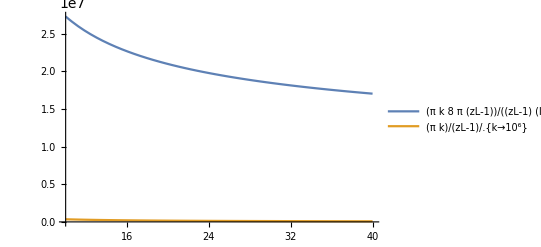

```mathematica
g2sol = 4 π / 10;
mKK5 = 
Plot[{π k /(zL-1)*8π (zL-1)/(Log[zL] * g2)/.{g2->g2sol, k->10^6},π k /(zL-1)/.{k->10^6}}, {zL, 10, 40}, PlotLegends->"Expressions"]
```

```mathematica
(*Initial beta function for QEM*)
```

```mathematica
classDict=<|"Electron"->       <|
					"GSMCharges"-><|"SU3C"->1,  "U1EM"->  <|"QEM" -> -1, "T3"-> -1/2|> |> ,
					"GammaFact"->8, "Families"->3
				     |> ,
	               ".7fDown"-> <|
					  "GSMCharges"-><|"SU3C"->3,  "U1EM"->  <|"QEM" -> -1/3, "T3"->-1/2|>  |>  ,
					"GammaFact"->8, "Families"->3
				      |>,
                       "Up"->         <|
					  "GSMCharges"-><|"SU3C"->3,  "U1EM"->  <|"QEM" -> 2/3, "T3"-> +1/2|>  |> ,
					"GammaFact"->8, "Families"->3
				       |>
,
		    "W-"->        <|
					 "GSMCharges"-><|"SU3C"->1,  "U1EM"->  <|"QEM" -> -1, "T3"-> -1|>  |> ,
					"GammaFact"->-22, "Families"->1
					|>
,
		    "W+"->        <|
					 "GSMCharges"-><|"SU3C"->1,  "U1EM"->  <|"QEM" -> +1, "T3"-> +1|>  |> ,
					"GammaFact"->-22, "Families"->1
					|>
,
		    "Higgs+"->        <|
					 "GSMCharges"-><|"SU3C"->1,  "U1EM"->  <|"QEM" -> +1, "T3"-> +1|>  |> ,
					"GammaFact"->1, "Families"->1
					|>
,      "Higgs-"->        <|
					 "GSMCharges"-><|"SU3C"->1,  "U1EM"->  <|"QEM" -> -1, "T3"-> +1|>  |> ,
					"GammaFact"->1, "Families"->1
					|>

|>;
(*NOTE , we don't need to include the Z^0, Higgs and neutrino since they have EM charge 0*)
SMfields = Keys[classDict];
sin2ThW = 0.2312;

betaCoef=0;
sin2ThWCoeff = 0;
sin2ThWCoeff2 = 0;

For[i=1, i≤ Length[SMfields], i++,
fieldToAdd = SMfields[[i]];
QCDcharge = classDict[fieldToAdd]["GSMCharges"]["SU3C"];
QEDcharge = classDict[fieldToAdd]["GSMCharges"]["U1EM"]["QEM"];
γFact =  classDict[fieldToAdd]["GammaFact"];
familyFact =   classDict[fieldToAdd]["Families"];

T3Coeff = classDict[fieldToAdd]["GSMCharges"]["U1EM"]["T3"];



betaCoef = betaCoef + (QCDcharge * γFact * (QEDcharge)^2 )*  familyFact;
sin2ThWCoeff =  sin2ThWCoeff + (QCDcharge * γFact * QEDcharge )*(T3Coeff - QEDcharge * sin2ThW)* familyFact;

Print[fieldToAdd, "  ",betaCoef];
]
Print[betaCoef]
Print[sin2ThWCoeff]
```

Electron  24

.7fDown  32

Up  64

W-  42

W+  20

Higgs+  21

Higgs-  22

22

-1.0864